## Canonicity factors

Creating proper inertia factors A_2 and A_3 from the value of A_1

```mathematica
ClearAll["Global`*"]
```

```mathematica
T[j_,gm_]:=1/(j(j+1))√3(√3 Cos[gm]+Sin[gm]);
TP[j_,gm_]:=1/(j(j+1))2 √3 Sin[gm];
S[I_,j_]:=(2I-1-2j)/(2I-1);
SP[I_,j_]:=(2j-1-2I)/(2j-1);
```

```mathematica
A3condition[A1_,I_,j_,V_,gm_]:=(SP[I,j]*A1-V*T[j,gm]);
A2condition[A1_,I_,j_,V_,gm_]:=(SP[I,j]*A1-V*TP[j,gm]);
```

```mathematica
A1=0.02;
I0=35/2;
j0=13/2;
V0=3;
gm0=25;
A2test1[I_,j_]:=Abs[A2condition[A1,I,j,V0,gm0*π/180]];
A3test1[I_,j_]:=Abs[A3condition[A1,I,j,V0,gm0*π/180]];
A2test2[I_,j_]:=Abs[A3condition[A1,I,j,V0,gm0*π/180]];
A3test2[I_,j_]:=Abs[A2condition[A1,I,j,V0,gm0*π/180]];
```

```mathematica
k1[I_,j_,A1_,A2_,A3_]:=(I^2*((2I-1)(A2-A1)+2j*A1)/((2I-1)(A3-A1)+2j*A1))^(1/4);
(*k1[35/2,j0,A1,A2test1[35/2,j0],A3test1[35/2,j0]]
k1[35/2,j0,A1,A2test2[35/2,j0],A3test2[35/2,j0]]*)
(*A2test1[35/2,j0]
A3test1[35/2,j0]
A2test2[35/2,j0]
A3test2[35/2,j0]*)
```

## Generate lists for numerical data

```mathematica
(*the data set for ordering A3>A2>A1 *)
k1data1=Table[{x,k1[x,j0,A1,A2test1[x,j0],A3test1[x,j0]]},{x,0.5,45.5,2}];
(*the data set for ordering A2>A3>A1 *)
k1data2=Table[{x,k1[x,j0,A1,A2test2[x,j0],A3test2[x,j0]]},{x,0.5,45.5,2}];
```

```mathematica
k1plot=ListPlot[{k1data1,k1data2},AspectRatio->0.8,Frame->True,Joined->True,PlotMarkers->{Automatic, Medium},FrameStyle->Directive[Black,Thick],PlotStyle->{{Red,Thick},{Blue,Thick}},PlotRange->Full,FrameLabel->{"I [ℏ]","k_1"},LabelStyle->{18,Bold,Black,FontFamily->"Arial"},ImageSize->380,PlotLegends->Placed[{"A_3>A_2>A_1","A_2>A_3>A_1"},{0.75,0.3}]];
k1fig=Show[k1plot,Graphics[{Magenta,Thick,Dashed,Line[{{13/2,0},{13/2,8}}]}],Graphics[{Green,HatchFilling[-1],Opacity[0.4],Rectangle[{-1,-1},{13/2,8}]}],Graphics[{Green,Opacity[0.15],Rectangle[{13/2,-1},{50,8}]}],Graphics[Inset[Style["I ≤ j",Black,Bold,FontFamily->"Palatino",21],Scaled[{0.08,0.8}]]],Graphics[Inset[Style["I ≥ j",Black,Bold,FontFamily->"Palatino",21],Scaled[{0.3,0.8}]]]];
Export["/Users/basavyr/Documents/Work/DFT/mathematica-useful-algorithms/Physics/wobbling-frequency-algebraic/k1_factor.pdf",k1fig];
k1fig
```

-Graphics-

### k1[I_,j_,A1_,A2_,A3_]:=(I^2*((2I-1)(A2-A1)+2j*A1)/((2I-1)(A3-A1)+2j*A1))^(1/4);

```mathematica
A3extended[I_,j_,V_,gm_]:=SP[I,j]*A1-V*T[j,gm];
A2extended[I_,j_,V_,gm_]:=SP[I,j]*A1-V*TP[j,gm];
k2[I_,j_,A1_,A2_,A3_,V_,gm_]:=(j^2*((2j-1)(A2-A1)+2I*A1+V*(2j-1)/(j(j+1))2 √3 Sin[gm])/((2j-1)(A3-A1)+2I*A1+V*(2j-1)/(j(j+1))√3(√3 Cos[gm]+Sin[gm])))^(1/4);
Abs[A3extended[I0,j0,V0,gm0*π/180]]
Abs[A2extended[I0,j0,V0,gm0*π/180]]
k2[x,j0,A1,A2extended[I0,j0,V0,gm0*π/180],A3extended[I0,j0,V0,gm0*π/180],V0,gm0*π/180]
```

0.250698

0.128425

√(13/2)

## Generate the numerical data

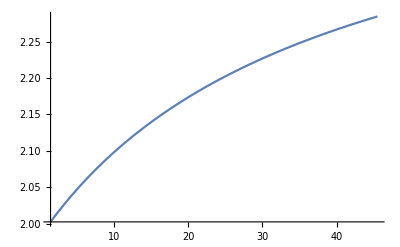

-Graphics-

```mathematica
Plot[k2[x,j0,A1,Abs[A2extended[x,j0,V0,gm0*π/180]],Abs[A3extended[x,j0,V0,gm0*π/180]],V0,gm0*π/180],{x,1.5,45.5}]
Plot[k2[x,j0,A1,Abs[A3extended[x,j0,V0,gm0*π/180]],Abs[A2extended[x,j0,V0,gm0*π/180]],V0,gm0*π/180],{x,1.5,45.5}]
```

```mathematica
k2data1=Table[{x,k2[x,j0,A1,Abs[A2extended[x,j0,V0,gm0*π/180]],Abs[A3extended[x,j0,V0,gm0*π/180]],V0,gm0*π/180]},{x,1.5,45.5,1}];
k2data1
```

{{1.5,2.00234},{2.5,2.01574},{3.5,2.02846},{4.5,2.04054},{5.5,2.05204},{6.5,2.063},{7.5,2.07346},{8.5,2.08345},{9.5,2.09302},{10.5,2.10217},{11.5,2.11095},{12.5,2.11938},{13.5,2.12747},{14.5,2.13526},{15.5,2.14274},{16.5,2.14996},{17.5,2.15691},{18.5,2.16361},{19.5,2.17009},{20.5,2.17634},{21.5,2.18238},{22.5,2.18822},{23.5,2.19388},{24.5,2.19935},{25.5,2.20466},{26.5,2.2098},{27.5,2.21479},{28.5,2.21963},{29.5,2.22432},{30.5,2.22889},{31.5,2.23332},{32.5,2.23763},{33.5,2.24182},{34.5,2.2459},{35.5,2.24987},{36.5,2.25373},{37.5,2.2575},{38.5,2.26116},{39.5,2.26474},{40.5,2.26822},{41.5,2.27162},{42.5,2.27494},{43.5,2.27818},{44.5,2.28134},{45.5,2.28443}}